# Data Analysis: Autosomal

## Data Pre - Processing

Load

```mathematica
SetDirectory["/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/ProcessedData"];
experimentsFolder="/Autosomal/";
fileNames=FileNames["E*.csv",Directory[]<>experimentsFolder];
```

```mathematica
header=Import[fileNames[[1]]][[1]];
rawData=(Import[#][[2;;All]])&/@fileNames;
flattenedData=ToExpression/@Flatten[rawData,1];
```

```mathematica
{header,Range[header//Length]}//Transpose//Grid[#,Frame->All]&
experimentsIDVectors=Cases[flattenedData,{homing_,femaleDep_,hFitness_,bFitness_,___}->{homing,femaleDep,hFitness,bFitness}];
Grid[{
header[[1;;4]],
(experimentsIDVectors[[All,#]]//DeleteDuplicates//Sort)&/@Range[4]
}//Transpose,Frame->All
]
```

Homing | 1
FemaleDeposition | 2
HFitness | 3
BFitness | 4
Day | 5
H | 6
W | 7
R | 8
B | 9

Homing | {0.65,0.7,0.75,0.8,0.85,0.9,0.95,0.99}
FemaleDeposition | {0.,0.25,0.5,0.75}
HFitness | {0.,0.02,0.04,0.06,0.08,0.1}
BFitness | {0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4}

Pre - Process

```mathematica
maxDay=flattenedData[[All,5]]//Max;
maxTotalPop=Max[Total/@flattenedData[[All,6;;8]]];
maxAllelePop=Max[Max/@flattenedData[[All,6;;8]]];
```

```mathematica
reShapedData={
#[[1]],#[[2]],#[[3]],#[[4]],
#[[5]]//Round,
#[[6]]/maxTotalPop,
#[[7]]/maxTotalPop,
#[[8]]/maxTotalPop,
#[[9]]/maxTotalPop
}&/@flattenedData;
```

```mathematica
dayProbed=999;
probedData=Cases[reShapedData,{homing_,femaleDep_,hFitness_,bFitness_,dayProbed,h_,w_,r_,b_}->{homing,femaleDep,hFitness,bFitness,h/(h+w+r+b)}];
```

## Analyze

```mathematica
USER=1;
If[USER==1,SetDirectory["/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR"],0];
If[USER==2,SetDirectory["/Volumes/Pusheen/MGDrivE_Experiments/MCR"],0];
```

Reshape into I/O

```mathematica
outInDataForm=(#[[5]]->{#[[1]],#[[2]],#[[3]],#[[4]]})&/@probedData;
inOutDataForm=({#[[1]],#[[2]],#[[3]],#[[4]]}->#[[5]])&/@probedData;
```

Find Clusters (Exploratory)

```mathematica
clusters=FindClusters[inOutDataForm];
Length[clusters]
```

5

{{0.65,0.,0.,0.25,0.915922},{0.65,0.,0.,0.3,0.896274},{0.65,0.,0.,0.35,0.924923},{0.65,0.,0.,0.4,0.914792},{0.65,0.,0.02,0.25,0.894119},{0.65,0.,0.02,0.3,0.897491},{0.65,0.,0.02,0.35,0.893245},{0.65,0.,0.02,0.4,0.897337},{0.65,0.,0.04,0.25,0.857352},{0.65,0.,0.04,0.3,0.834875},{0.65,0.,0.04,0.35,0.863694},{0.65,0.,0.04,0.4,0.854458},{0.65,0.,0.06,0.25,0.797093},{0.65,0.,0.06,0.3,0.805013},{0.65,0.,0.06,0.35,0.818541},{0.65,0.,0.06,0.4,0.816733},{0.65,0.,0.08,0.25,0.752561},{0.65,0.,0.08,0.3,0.765293},{0.65,0.,0.08,0.35,0.774081},{0.65,0.,0.08,0.4,0.796977},{0.65,0.,0.1,0.25,0.689003},{0.65,0.,0.1,0.3,0.726652},{0.65,0.,0.1,0.35,0.716713},{0.65,0.,0.1,0.4,0.728211},{0.65,0.25,0.,0.4,0.914078},{0.65,0.25,0.02,0.35,0.877571},{0.65,0.25,0.02,0.4,0.862945},{0.65,0.25,0.04,0.3,0.821182},{0.65,0.25,0.04,0.35,0.816152},{0.65,0.25,0.04,0.4,0.83766},{0.65,0.25,0.06,0.25,0.768408},{0.65,0.25,0.06,0.3,0.728644},{0.65,0.25,0.06,0.35,0.753698},{0.65,0.25,0.06,0.4,0.778355},{0.65,0.25,0.08,0.35,0.745177},{0.65,0.25,0.08,0.4,0.745098},{0.65,0.25,0.1,0.4,0.67359},{0.7,0.,0.,0.25,0.941304},{0.7,0.,0.,0.3,0.940289},{0.7,0.,0.,0.35,0.936698},{0.7,0.,0.,0.4,0.932209},{0.7,0.,0.02,0.25,0.907189},{0.7,0.,0.02,0.3,0.915638},{0.7,0.,0.02,0.35,0.91932},{0.7,0.,0.02,0.4,0.918365},{0.7,0.,0.04,0.25,0.862963},{0.7,0.,0.04,0.3,0.894709},{0.7,0.,0.04,0.35,0.879513},{0.7,0.,0.04,0.4,0.884498},{0.7,0.,0.06,0.25,0.819583},{0.7,0.,0.06,0.3,0.851823},{0.7,0.,0.06,0.35,0.854713},{0.7,0.,0.06,0.4,0.845825},{0.7,0.,0.08,0.25,0.792118},{0.7,0.,0.08,0.3,0.809547},{0.7,0.,0.08,0.35,0.801973},{0.7,0.,0.08,0.4,0.830012},{0.7,0.,0.1,0.25,0.72521},{0.7,0.,0.1,0.3,0.742754},{0.7,0.,0.1,0.35,0.746513},{0.7,0.,0.1,0.4,0.775122},{0.7,0.25,0.,0.35,0.919504},{0.7,0.25,0.,0.4,0.924555},{0.7,0.25,0.02,0.3,0.882903},{0.7,0.25,0.02,0.35,0.897545},{0.7,0.25,0.02,0.4,0.864781},{0.7,0.25,0.04,0.25,0.845739},{0.7,0.25,0.04,0.3,0.802024},{0.7,0.25,0.04,0.35,0.87164},{0.7,0.25,0.04,0.4,0.848537},{0.7,0.25,0.06,0.25,0.801785},{0.7,0.25,0.06,0.3,0.795622},{0.7,0.25,0.06,0.35,0.812734},{0.7,0.25,0.06,0.4,0.821356},{0.7,0.25,0.08,0.3,0.758842},{0.7,0.25,0.08,0.35,0.753351},{0.7,0.25,0.08,0.4,0.783537},{0.7,0.25,0.1,0.4,0.701753},{0.7,0.5,0.06,0.4,0.749375},{0.75,0.,0.,0.25,0.946806},{0.75,0.,0.,0.3,0.949709},{0.75,0.,0.,0.35,0.949244},{0.75,0.,0.,0.4,0.945909},{0.75,0.,0.02,0.25,0.932292},{0.75,0.,0.02,0.3,0.927184},{0.75,0.,0.02,0.35,0.937315},{0.75,0.,0.02,0.4,0.928574},{0.75,0.,0.04,0.25,0.910476},{0.75,0.,0.04,0.3,0.903821},{0.75,0.,0.04,0.35,0.907655},{0.75,0.,0.04,0.4,0.911183},{0.75,0.,0.06,0.25,0.85208},{0.75,0.,0.06,0.3,0.850157},{0.75,0.,0.06,0.35,0.878254},{0.75,0.,0.06,0.4,0.898596},{0.75,0.,0.08,0.25,0.824451},{0.75,0.,0.08,0.3,0.819997},{0.75,0.,0.08,0.35,0.849208},{0.75,0.,0.08,0.4,0.850464},{0.75,0.,0.1,0.25,0.781778},{0.75,0.,0.1,0.3,0.798574},{0.75,0.,0.1,0.35,0.791257},{0.75,0.,0.1,0.4,0.805801},{0.75,0.25,0.,0.3,0.911951},{0.75,0.25,0.,0.35,0.931844},{0.75,0.25,0.,0.4,0.939449},{0.75,0.25,0.02,0.25,0.904033},{0.75,0.25,0.02,0.3,0.910112},{0.75,0.25,0.02,0.35,0.916922},{0.75,0.25,0.02,0.4,0.926936},{0.75,0.25,0.04,0.25,0.882426},{0.75,0.25,0.04,0.3,0.883283},{0.75,0.25,0.04,0.35,0.863523},{0.75,0.25,0.04,0.4,0.882876},{0.75,0.25,0.06,0.25,0.826499},{0.75,0.25,0.06,0.3,0.8597},{0.75,0.25,0.06,0.35,0.847779},{0.75,0.25,0.06,0.4,0.852094},{0.75,0.25,0.08,0.25,0.799044},{0.75,0.25,0.08,0.3,0.766375},{0.75,0.25,0.08,0.35,0.795755},{0.75,0.25,0.08,0.4,0.828268},{0.75,0.25,0.1,0.35,0.781041},{0.75,0.25,0.1,0.4,0.764299},{0.75,0.5,0.06,0.4,0.774147},{0.8,0.,0.,0.25,0.952956},{0.8,0.,0.,0.3,0.961259},{0.8,0.,0.,0.35,0.966187},{0.8,0.,0.,0.4,0.964463},{0.8,0.,0.02,0.25,0.945465},{0.8,0.,0.02,0.3,0.943497},{0.8,0.,0.02,0.35,0.95351},{0.8,0.,0.02,0.4,0.960705},{0.8,0.,0.04,0.25,0.927163},{0.8,0.,0.04,0.3,0.928826},{0.8,0.,0.04,0.35,0.933206},{0.8,0.,0.04,0.4,0.927387},{0.8,0.,0.06,0.25,0.893177},{0.8,0.,0.06,0.3,0.902497},{0.8,0.,0.06,0.35,0.905747},{0.8,0.,0.06,0.4,0.89274},{0.8,0.,0.08,0.25,0.837883},{0.8,0.,0.08,0.3,0.870736},{0.8,0.,0.08,0.35,0.867227},{0.8,0.,0.08,0.4,0.876146},{0.8,0.,0.1,0.25,0.815124},{0.8,0.,0.1,0.3,0.812984},{0.8,0.,0.1,0.35,0.806124},{0.8,0.,0.1,0.4,0.822441},{0.8,0.25,0.,0.3,0.947327},{0.8,0.25,0.,0.35,0.956409},{0.8,0.25,0.,0.4,0.953657},{0.8,0.25,0.02,0.25,0.929481},{0.8,0.25,0.02,0.3,0.924416},{0.8,0.25,0.02,0.35,0.925792},{0.8,0.25,0.02,0.4,0.939547},{0.8,0.25,0.04,0.25,0.904796},{0.8,0.25,0.04,0.3,0.907953},{0.8,0.25,0.04,0.35,0.887144},{0.8,0.25,0.04,0.4,0.893538},{0.8,0.25,0.06,0.25,0.863259},{0.8,0.25,0.06,0.3,0.883701},{0.8,0.25,0.06,0.35,0.854501},{0.8,0.25,0.06,0.4,0.879701},{0.8,0.25,0.08,0.25,0.834269},{0.8,0.25,0.08,0.3,0.855617},{0.8,0.25,0.08,0.35,0.840483},{0.8,0.25,0.08,0.4,0.860453},{0.8,0.25,0.1,0.3,0.785641},{0.8,0.25,0.1,0.35,0.777278},{0.8,0.25,0.1,0.4,0.79917},{0.8,0.5,0.04,0.4,0.874793},{0.8,0.5,0.06,0.35,0.840049},{0.8,0.5,0.06,0.4,0.831919},{0.8,0.5,0.08,0.4,0.730593},{0.85,0.,0.,0.25,0.972354},{0.85,0.,0.,0.3,0.974486},{0.85,0.,0.,0.35,0.968943},{0.85,0.,0.,0.4,0.974274},{0.85,0.,0.02,0.25,0.955141},{0.85,0.,0.02,0.3,0.960896},{0.85,0.,0.02,0.35,0.963319},{0.85,0.,0.02,0.4,0.969086},{0.85,0.,0.04,0.25,0.935179},{0.85,0.,0.04,0.3,0.958761},{0.85,0.,0.04,0.35,0.954429},{0.85,0.,0.04,0.4,0.946384},{0.85,0.,0.06,0.25,0.913386},{0.85,0.,0.06,0.3,0.941346},{0.85,0.,0.06,0.35,0.924935},{0.85,0.,0.06,0.4,0.924145},{0.85,0.,0.08,0.25,0.909119},{0.85,0.,0.08,0.3,0.911408},{0.85,0.,0.08,0.35,0.917746},{0.85,0.,0.08,0.4,0.906596},{0.85,0.,0.1,0.25,0.860769},{0.85,0.,0.1,0.3,0.875105},{0.85,0.,0.1,0.35,0.881765},{0.85,0.,0.1,0.4,0.892341},{0.85,0.25,0.,0.25,0.957769},{0.85,0.25,0.,0.3,0.968079},{0.85,0.25,0.,0.35,0.958182},{0.85,0.25,0.,0.4,0.965812},{0.85,0.25,0.02,0.25,0.948615},{0.85,0.25,0.02,0.3,0.938479},{0.85,0.25,0.02,0.35,0.926096},{0.85,0.25,0.02,0.4,0.943431},{0.85,0.25,0.04,0.25,0.922881},{0.85,0.25,0.04,0.3,0.902344},{0.85,0.25,0.04,0.35,0.920983},{0.85,0.25,0.04,0.4,0.936855},{0.85,0.25,0.06,0.25,0.87376},{0.85,0.25,0.06,0.3,0.876405},{0.85,0.25,0.06,0.35,0.907302},{0.85,0.25,0.06,0.4,0.901778},{0.85,0.25,0.08,0.25,0.862535},{0.85,0.25,0.08,0.3,0.875469},{0.85,0.25,0.08,0.35,0.871422},{0.85,0.25,0.08,0.4,0.857585},{0.85,0.25,0.1,0.3,0.835881},{0.85,0.25,0.1,0.35,0.847781},{0.85,0.25,0.1,0.4,0.852026},{0.85,0.5,0.02,0.4,0.910745},{0.85,0.5,0.04,0.4,0.911844},{0.85,0.5,0.06,0.35,0.861048},{0.85,0.5,0.06,0.4,0.853777},{0.85,0.5,0.08,0.4,0.844272},{0.9,0.,0.,0.25,0.981215},{0.9,0.,0.,0.3,0.984233},{0.9,0.,0.,0.35,0.984559},{0.9,0.,0.,0.4,0.979512},{0.9,0.,0.02,0.25,0.972662},{0.9,0.,0.02,0.3,0.954483},{0.9,0.,0.02,0.35,0.977155},{0.9,0.,0.02,0.4,0.979923},{0.9,0.,0.04,0.25,0.95952},{0.9,0.,0.04,0.3,0.967095},{0.9,0.,0.04,0.35,0.959076},{0.9,0.,0.04,0.4,0.967192},{0.9,0.,0.06,0.25,0.943432},{0.9,0.,0.06,0.3,0.952998},{0.9,0.,0.06,0.35,0.960206},{0.9,0.,0.06,0.4,0.953316},{0.9,0.,0.08,0.25,0.939999},{0.9,0.,0.08,0.3,0.939031},{0.9,0.,0.08,0.35,0.936739},{0.9,0.,0.08,0.4,0.936725},{0.9,0.,0.1,0.25,0.913635},{0.9,0.,0.1,0.3,0.923736},{0.9,0.,0.1,0.35,0.903879},{0.9,0.,0.1,0.4,0.919083},{0.9,0.25,0.,0.25,0.970669},{0.9,0.25,0.,0.3,0.96834},{0.9,0.25,0.,0.35,0.97608},{0.9,0.25,0.,0.4,0.976372},{0.9,0.25,0.02,0.25,0.96534},{0.9,0.25,0.02,0.3,0.970807},{0.9,0.25,0.02,0.35,0.954644},{0.9,0.25,0.02,0.4,0.963763},{0.9,0.25,0.04,0.25,0.949679},{0.9,0.25,0.04,0.3,0.943451},{0.9,0.25,0.04,0.35,0.945213},{0.9,0.25,0.04,0.4,0.959131},{0.9,0.25,0.06,0.25,0.915574},{0.9,0.25,0.06,0.3,0.924779},{0.9,0.25,0.06,0.35,0.93328},{0.9,0.25,0.06,0.4,0.924994},{0.9,0.25,0.08,0.25,0.908999},{0.9,0.25,0.08,0.3,0.90089},{0.9,0.25,0.08,0.35,0.920485},{0.9,0.25,0.08,0.4,0.9125},{0.9,0.25,0.1,0.25,0.868985},{0.9,0.25,0.1,0.3,0.876073},{0.9,0.25,0.1,0.35,0.860939},{0.9,0.25,0.1,0.4,0.876223},{0.95,0.,0.,0.25,0.9923},{0.95,0.,0.,0.3,0.989836},{0.95,0.,0.,0.35,0.98965},{0.95,0.,0.,0.4,0.990865},{0.95,0.,0.02,0.25,0.987864},{0.95,0.,0.02,0.3,0.992209},{0.95,0.,0.02,0.35,0.991252},{0.95,0.,0.02,0.4,0.987899},{0.95,0.,0.04,0.25,0.984754},{0.95,0.,0.04,0.3,0.97909},{0.95,0.,0.04,0.35,0.980726},{0.95,0.,0.04,0.4,0.982299},{0.95,0.,0.06,0.25,0.977578},{0.95,0.,0.06,0.3,0.957967},{0.95,0.,0.06,0.35,0.981926},{0.95,0.,0.06,0.4,0.98093},{0.95,0.,0.08,0.25,0.972215},{0.95,0.,0.08,0.3,0.96925},{0.95,0.,0.08,0.35,0.96738},{0.95,0.,0.08,0.4,0.973079},{0.95,0.,0.1,0.25,0.951909},{0.95,0.,0.1,0.3,0.955986},{0.95,0.,0.1,0.35,0.94768},{0.95,0.,0.1,0.4,0.950505},{0.95,0.25,0.,0.3,0.984266},{0.95,0.25,0.,0.35,0.9773},{0.95,0.25,0.,0.4,0.987972},{0.95,0.25,0.02,0.3,0.973237},{0.95,0.25,0.02,0.35,0.981612},{0.95,0.25,0.02,0.4,0.975365},{0.95,0.25,0.04,0.3,0.962311},{0.95,0.25,0.04,0.35,0.942382},{0.95,0.25,0.04,0.4,0.966426},{0.95,0.25,0.06,0.3,0.954403},{0.95,0.25,0.06,0.35,0.95008},{0.95,0.25,0.06,0.4,0.941096},{0.95,0.25,0.08,0.3,0.931491},{0.95,0.25,0.08,0.35,0.937733},{0.95,0.25,0.08,0.4,0.938886},{0.95,0.25,0.1,0.3,0.861756},{0.95,0.25,0.1,0.35,0.922292},{0.95,0.25,0.1,0.4,0.931256},{0.99,0.,0.,0.25,0.998988},{0.99,0.,0.,0.3,0.999006},{0.99,0.,0.,0.35,0.998307},{0.99,0.,0.,0.4,0.972804},{0.99,0.,0.02,0.25,0.997779},{0.99,0.,0.02,0.3,0.999004},{0.99,0.,0.02,0.35,0.998768},{0.99,0.,0.02,0.4,0.996814},{0.99,0.,0.04,0.25,0.99917},{0.99,0.,0.04,0.3,0.998477},{0.99,0.,0.04,0.35,0.997528},{0.99,0.,0.04,0.4,0.99806},{0.99,0.,0.06,0.25,0.993003},{0.99,0.,0.06,0.3,0.995973},{0.99,0.,0.06,0.35,0.997588},{0.99,0.,0.06,0.4,0.996583},{0.99,0.,0.08,0.25,0.995144},{0.99,0.,0.08,0.3,0.971262},{0.99,0.,0.08,0.35,0.996012},{0.99,0.,0.08,0.4,0.996169},{0.99,0.,0.1,0.25,0.994889},{0.99,0.,0.1,0.3,0.994883},{0.99,0.,0.1,0.35,0.993259},{0.99,0.,0.1,0.4,0.988958},{0.99,0.25,0.,0.35,0.993535},{0.99,0.25,0.,0.4,0.989537},{0.99,0.25,0.02,0.35,0.988713},{0.99,0.25,0.02,0.4,0.983493},{0.99,0.25,0.04,0.35,0.97811},{0.99,0.25,0.04,0.4,0.979697},{0.99,0.25,0.06,0.35,0.945312},{0.99,0.25,0.06,0.4,0.976247},{0.99,0.25,0.08,0.35,0.937515},{0.99,0.25,0.08,0.4,0.970119},{0.99,0.25,0.1,0.35,0.945815},{0.99,0.25,0.1,0.4,0.946617}}

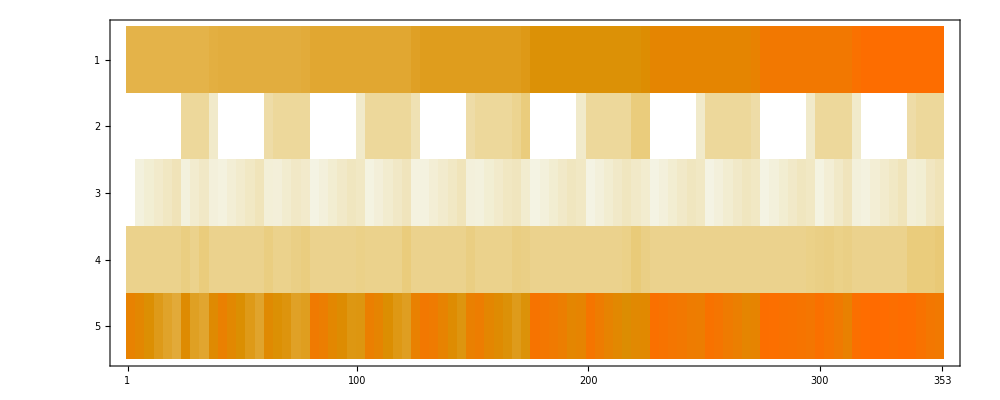

```mathematica
clusterToInspect=2;
clusteredData=Flatten[Cases[outInDataForm,(#->a_)->{a,#}]&/@clusters[[clusterToInspect]],1];
Flatten/@clusteredData
MatrixPlot[%//Transpose,ImageSize->1000]
```

Machine Learning (Predictive)

## One - Fold

Setting up training and validation sets

```mathematica
validationFraction=.8;
samplesNumber=(inOutDataForm//Length);
trainingIndex=samplesNumber*validationFraction//Round;

sample=RandomSample[inOutDataForm];
training=sample[[1;;trainingIndex]];
validation=sample[[(trainingIndex+1);;samplesNumber]];
```

Training and testing

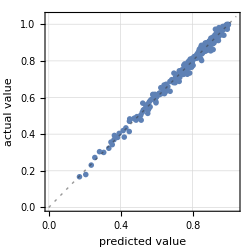
Predictor information
Input type | NumericalVector (length: 4)
Method | GaussianProcess
Standard deviation | 0.0346 ± 0.0027
Loss | 0.00368 ± 0.057
Single evaluation time | 5.85 ms/example
Batch evaluation speed | 7.35 examples/ms
Predictor memory | 12.3 MB
Training examples used | 1228 examples
Training time | 20.5 s
 |  | Predictor Measurements
Number of test examples | 307
Standard deviation | 0.0158 ± 0.0008
Standard deviation baseline | 0.172 ± 0.0086
Mean cross entropy | -1.08 ± 0.31
Single evaluation time | 5.99 ms/example
Batch evaluation speed | 1.8 examples/ms
-Graphics- |

```mathematica
predictionFunction=Predict[training
,ValidationSet->validation
,PerformanceGoal->"Quality"
,Method->"GaussianProcess"
];
Grid[{{
PredictorInformation[predictionFunction],
PredictorMeasurements[predictionFunction,validation, "Report"]
}}]
```

Sensitivity Analysis

## Raw Data

```mathematica
experimentName="ProcessedData/Autosomal";
directoryData=Directory[]<>"/"<>experimentName<>"/";
sampledData=Import[directoryData<>#<>"processedData.csv"][[2;;All]]&/@{"E_065","E_070","E_075","E_080","E_085","E_090","E_095","E_099"};
flattenedData=Flatten[sampledData,1];
maxPop=Max[flattenedData[[All,6;;9]]];
levels=DeleteDuplicates/@(flattenedData[[All,1;;4]]//Transpose);
days=flattenedData[[All,5]]//DeleteDuplicates;
```

### One Sphere

```mathematica
{day,homingRate,wThreshold}={999,.75,{0,1}};
rescaled={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]/maxPop,#[[7]]/maxPop,#[[8]]/maxPop,#[[9]]/maxPop}&/@flattenedData;
filtered=Cases[rescaled,({homingRate,fd_,hc_,bc_,days[[day]],h_,w_,r_,b_})->{fd,hc,bc,h}];
```

```mathematica
ListSliceContourPlot3D[filtered,
{"CenterCutSphere",100Degree,45Degree}
,AxesLabel->(Style[#,35]&/@{"F","H","B"})
,BoxRatios->{1,1,1}
,BoxStyle->Directive[Thick]
,ColorFunction->ColorData[{"DeepSeaColors",{.5,1}}]
,ColorFunctionScaling->False
,Contours->10
,ContourStyle->Directive[Black,Thick]
(*,FaceGrids->{{0,1,0},{0,0,-1},{-1,0,0}}
,FaceGridsStyle->Directive[Opacity[.2],Thick]*)
,ImageSize->1250
,PerformanceGoal->Automatic
,PlotLabel->Style["Homing Rate: "<>ToString[homingRate],75]
,PlotLegends->Automatic
,Ticks->Automatic
,TicksStyle->25
,ViewPoint->{2,2,-.25}
];
Show[%,Graphics3D[{AbsolutePointSize[10],Opacity[.25],Black,Point[filtered[[All,1;;3]]]}]]
```

-Graphics3D-

### All Spheres

```mathematica
homingRates=((experimentsIDVectors[[All,#]]//DeleteDuplicates//Sort)&/@Range[4])[[1]];
plots=Table[
{day,homingRate,wThreshold}={999,i,{0,1}};
rescaled={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]/maxPop,#[[7]]/maxPop,#[[8]]/maxPop,#[[9]]/maxPop}&/@flattenedData;
filtered=Cases[rescaled,({homingRate,fd_,hc_,bc_,days[[day]],h_,w_,r_,b_})->{fd,hc,bc,h}];
fa=ListSliceContourPlot3D[filtered,
"CenterSphere"
,AxesLabel->(Style[#,35]&/@{"F_d","H_c","B_c"})
,BoxRatios->{1,1,1}
,BoxStyle->Directive[Thick]
,ColorFunction->ColorData[{"DeepSeaColors",{.5,1}}]
,ColorFunctionScaling->False
,Contours->10
,ContourStyle->Directive[Black,Thick]
(*,FaceGrids->{{0,1,0},{0,0,-1},{-1,0,0}}
,FaceGridsStyle->Directive[Opacity[.2],Thick]*)
,ImageSize->750
,PerformanceGoal->Automatic
,PlotLabel->Style["Homing Rate: "<>ToString[homingRate],75]
,Ticks->Automatic
,TicksStyle->20
(*,ViewPoint->{2,2,-.25}*)
(*.1c,ViewPoint->{Bottom,Left}*)
]
,{i,homingRates}];
```

```mathematica
barLegend=BarLegend[{"DeepSeaColors",{.5,1}}
,LabelStyle->Directive[25]
,LegendLabel->Style["H",75,Black]
,LegendMarkerSize->750
];
```

```mathematica
spheresGrids=Grid[{{plots[[1]],plots[[2]],plots[[3]],plots[[4]],"         ",barLegend},{plots[[5]],plots[[6]],plots[[7]],plots[[8]],"         ",""}}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- |           | 
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- |           |

```mathematica
Export["SpheresPlots3.pdf",spheresGrids,ImageSize->5000,ImageResolution->300]
```

SpheresPlots3.pdf

## Machine Learning

```mathematica
Grid[{
header[[1;;4]],
(experimentsIDVectors[[All,#]]//DeleteDuplicates//Sort)&/@Range[4]
}//Transpose
,Frame->All
]
```

Homing | {0.65,0.7,0.75,0.8,0.85,0.9,0.95,0.99}
FemaleDeposition | {0.,0.25,0.5,0.75}
HFitness | {0.,0.02,0.04,0.06,0.08,0.1}
BFitness | {0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4}

```mathematica
homing=.75;
function1[x_]:=Blend[{Darker[White,0],Darker[Blue,.3],Darker[White,.0]},x]

DensityPlot3D[predictionFunction[{homing,fd,hf,bf}]
,{fd,0,.75}
,{hf,0,.1}
,{bf,0,.4}
,AxesLabel->(Style[#,35]&/@{"F","H","B"})
,BoxRatios->{1,1,1}
,BoxStyle->Directive[Thick]
,ColorFunction->function1
,ColorFunctionScaling->True
,FaceGrids->{{0,-1,0},{0,0,-1},{1,0,0}}
,FaceGridsStyle->Directive[Opacity[.2],Thick]
,ImageSize->750
,PerformanceGoal->"Speed"
,PlotLabel->Style["",75]
,OpacityFunction->Interval[{.2,1}]
,Ticks->Automatic
,TicksStyle->25
,ViewPoint->{-1.5,1.5,1.5}
]
```

-Graphics3D-